```mathematica
A[c_,s_,d_]:=a/2 c^2 - (1+a)/3 c^3 +1/4 c^4 +α s c^2-β/2 d c^2-rs/2 s^2+rs/3 s^3-δ/2 d s^2-rd/2 d^2+rd/3 d^3
```

```mathematica
cDot[c_,s_,d_]:=-D[A[c,s,d],c]
```

```mathematica
sDot[c_,s_,d_]:=-D[A[c,s,d],s]
```

```mathematica
iDot[c_,s_,d_]:=-D[A[c,s,d],d]
```

```mathematica
cDot[c,s,d]
```

-a c+(1+a) c^2-c^3-2 c s α+c d β

```mathematica
sDot[c,s,d]
```

rs s-rs s^2-c^2 α+d s δ

```mathematica
iDot[c,s,d]
```

d rd-d^2 rd+(c^2 β)/2+(s^2 δ)/2

```mathematica
sDesp=Solve[cDot[c,s,d]==0, s];
```

```mathematica
sDesp2= sDesp[[1]][[1]][[2]];
```

```mathematica
F1[c_,d_]:=FullSimplify[sDot[c,s,d]/.s ->sDesp2]
```

```mathematica
F2[c_,d_]:=FullSimplify[iDot[c,s,d]/.s ->sDesp2]
```

```mathematica
F1all[c_,d_,rc_,rs_,rd_,α_,δ_,β_,a_]=F1[c,d];
```

```mathematica
F2all[c_,d_,rc_,rs_,rd_,α_,δ_,β_,a_]=F2[c,d];
```

```mathematica
params=List[
rc1=0.03,
rs1=0.078,
rd1=1.256,
α1=0.95,
δ1=0.034,
β1=0.02,
a1= 0.2];
```

```mathematica
F1all[c,d,rc,rs,rd,α,δ,β,a]
```

(-4 c^2 α^3+2 rs α ((a-c) (-1+c)+d β)-rs ((a-c) (-1+c)+d β)^2+2 d α ((a-c) (-1+c)+d β) δ)/(4 α^2)

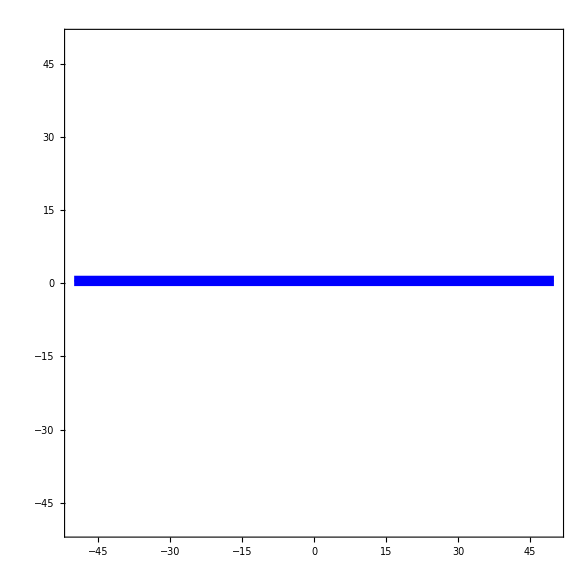
```mathematica
Manipulate[
Show[
{ContourPlot[
{F1all[c,d,rc,rs,rd,α,δ,β,a]==0,
F2all[c,d,rc,rs,rd,α,δ,β,a]==0},
{c,-50,50},
{d,-50,50},
PlotLegends->{Style["f1",25],Style["f2",25]},
ContourStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.007]}},
LabelStyle->Directive[Black,
FontFamily->"Helvetica",
FontSize->14]],
VectorPlot[-Graphics-
{F1all[c,d,rc,rs,rd,α,δ,β,a],
F2all[c,d,rc,rs,rd,α,δ,β,a]},
{c,-50,50},
{d,-50,50},
LabelStyle->Directive[Black,
FontFamily->"Helvetica",
FontSize->10],
VectorStyle->Arrowheads[0.03],
VectorPoints->12,
Axes->True,
AxesLabel->{Style["s",45,Gray],Style["i",45,Gray]}
]
}],
{{rc,params[[1]]},0,2},
{{rs,params[[2]]},0,2},
{{rd,params[[3]]},0,2},
{{α,params[[4]]},0,2},
{{δ,params[[5]]},0,2},
{{β,params[[6]]},0,2},
{{a,params[[7]]},0,2}]
```

```mathematica
F1[c,d]
```

(-4 c^2 α^3+2 rs α ((a-c) (-1+c)+d β)-rs ((a-c) (-1+c)+d β)^2+2 d α ((a-c) (-1+c)+d β) δ)/(4 α^2)

```mathematica
F2[c,d]
```

d rd-d^2 rd+(c^2 β)/2+(((a-c) (-1+c)+d β)^2 δ)/(8 α^2)

```mathematica
Solve[ Simplify[ Expand[ F1[c, d] ]] == 0 , c][[2,1]]
```

c→(1+a)/2-1/2 √((1+a)^2-(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)+(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/2 √(2 (1+a)^2-(4 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)-(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))-1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3)-(8 (1+a)^3-(8 (1+a) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/rs+(16 (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ))/rs)/(4 √((1+a)^2-(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)+(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))))

```mathematica
ssteady1[d_] = Collect[ c /. Solve[ Simplify[ Expand[ F1[c, d] ]] == 0 , c][[1, 1]], d]
```

1/2+a/2-1/2 √((1+a)^2-(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)+(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))-1/2 √(2 (1+a)^2-(4 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)-(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))-1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3)-(8 (1+a)^3-(8 (1+a) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/rs+(16 (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ))/rs)/(4 √((1+a)^2-(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)+(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))))

```mathematica
ssteady2[d_] = Collect[ c /. Solve[ Simplify[ Expand[ F1[c, d] ]] == 0 , c][[2, 1]], d]/□
```

1/□(1/2+a/2-1/2 √((1+a)^2-(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)+(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/2 √(2 (1+a)^2-(4 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)-(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))-1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3)-(8 (1+a)^3-(8 (1+a) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/rs+(16 (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ))/rs)/(4 √((1+a)^2-(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ))/(3 rs)+(2^(1/3) ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)))/(3 rs (2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3))+1/(3 2^(1/3) rs)(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)+√(-4 ((rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^2-12 (rs+a rs) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+12 rs (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^3+(2 (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ)^3-36 (rs+a rs) (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)+108 rs (a rs+a^2 rs+rs α+a rs α-d rs β-a d rs β+d α δ+a d α δ)^2+108 (rs+a rs)^2 (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ)-72 rs (rs+4 a rs+a^2 rs+2 rs α+4 α^3-2 d rs β+2 d α δ) (a^2 rs+2 a rs α-2 a d rs β-2 d rs α β+d^2 rs β^2+2 a d α δ-2 d^2 α β δ))^2))^(1/3)))))

```mathematica
ssteady3[d_] = Collect[ c /. Solve[ Simplify[ Expand[ F2[c, d] ]] == 0 , c][[1, 1]], d]
```

1/2+a/2-1/2 √((1+a)^2-(4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ)/δ-(-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)/(3 δ)-(2^(1/3) ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)))/(3 δ (2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))-1/(3 2^(1/3) δ)(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))-1/2 √(2 (1+a)^2-(4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ)/δ+(-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)/(3 δ)+(2^(1/3) ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)))/(3 δ (2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))+1/(3 2^(1/3) δ)(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3)-(8 (1+a)^3+16 (a+a^2-d β-a d β)-(8 (1+a) (4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ))/δ)/(4 √((1+a)^2-(4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ)/δ-(-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)/(3 δ)-(2^(1/3) ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)))/(3 δ (2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))-1/(3 2^(1/3) δ)(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))))

```mathematica
ssteady4[d_] = Collect[ c /. Solve[ Simplify[ Expand[ F2[c, d] ]] == 0 , c][[2, 1]], d]
```

1/2+a/2-1/2 √((1+a)^2-(4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ)/δ-(-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)/(3 δ)-(2^(1/3) ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)))/(3 δ (2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))-1/(3 2^(1/3) δ)(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))+1/2 √(2 (1+a)^2-(4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ)/δ+(-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)/(3 δ)+(2^(1/3) ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)))/(3 δ (2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))+1/(3 2^(1/3) δ)(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3)-(8 (1+a)^3+16 (a+a^2-d β-a d β)-(8 (1+a) (4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ))/δ)/(4 √((1+a)^2-(4 α^2 β+δ+4 a δ+a^2 δ-2 d β δ)/δ-(-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)/(3 δ)-(2^(1/3) ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)))/(3 δ (2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))-1/(3 2^(1/3) δ)(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+√(-4 ((-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^2-12 (δ+a δ) (a δ+a^2 δ-d β δ-a d β δ)-12 δ (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^3+(2 (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ)^3-36 (δ+a δ) (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (a δ+a^2 δ-d β δ-a d β δ)-108 δ (a δ+a^2 δ-d β δ-a d β δ)^2+108 (δ+a δ)^2 (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ)+72 δ (-4 α^2 β-δ-4 a δ-a^2 δ+2 d β δ) (-8 d rd α^2+8 d^2 rd α^2-a^2 δ+2 a d β δ-d^2 β^2 δ))^2))^(1/3))))

```mathematica
(*sintersec = Solve[ Simplify[ Expand[ ssteady1[d] ]] == ssteady3[d] , d];*)
```

```mathematica
(*sintersec2 = d /. sintersec ;*)
```

```mathematica
cDotLap[c_, s_, d_] = -Dc q^2 c + cDot[c, s, d];
```

```mathematica
sDotLap[c_, s_, d_] =  -Ds q^2 s + sDot[c, s, d];
```

```mathematica
iDotLap[c_, s_, d_] =  -Dd q^2 d + iDot[c, s, d] ;
```

```mathematica
cDot[c, s, d]
```

-a c+(1+a) c^2-c^3-2 c s α+c d β

```mathematica
Collect[
 Expand[ 
  Normal[ 
    Series[
     cDotLap[ c + δc,s + δs, d + δd],
      {δc, 0, 1}, {δs, 0, 1},{δd, 0, 1}
     ] 
    ] - cDotLap[c, s, d]
  ],
 {δc, δs, δd}
 ]
```

c β δd-2 c α δs+δc (-a+2 c+2 a c-3 c^2-Dc q^2-2 s α+d β+β δd-2 α δs)

```mathematica
c β δd-2 c α δs+δc (-a+2 c+2 a c-3 c^2-Dc q^2-2 s α+d β+β δd-2 α δs)
```

c β δd-2 c α δs+δc (-a+2 c+2 a c-3 c^2-Dc q^2-2 s α+d β+β δd-2 α δs)

```mathematica
Collect[
 Expand[ 
  Normal[ 
    Series[
     sDotLap[c + δd, s + δs, d + δd],
     {δc, 0, 1}, {δs, 0, 1}, {δd, 0, 1}
     ]
    ] - sDotLap[c, s, d]
  ],
 {δc, δs, δd}
 ]
```

(-2 c α+s δ) δd+(-Ds q^2+rs-2 rs s+d δ+δ δd) δs

```mathematica
Collect[
 Expand[ 
  Normal[ 
    Series[
     iDotLap[c + δc, s + δs, d + δd],
     {δc, 0, 1}, {δs, 0, 1}, {δd, 0, 1}
     ]
    ] - iDotLap[ c, s,d]
  ],
 { δc,δs, δd}
 ]
```

c β δc+(-Dd q^2+rd-2 d rd) δd+s δ δs

```mathematica
DynamicMatrix = {
  {-a+2 c+2 a c-3 c^2-Dc q^2-2 s α+d β, -2 c α , c β },
  {0,  -Ds q^2+rs-2 rs s+d δ,-2 c α+s δ},
  {c β , s δ , -Dd q^2+rd-2 d rd}
  }
```

{{-a+2 c+2 a c-3 c^2-Dc q^2-2 s α+d β,-2 c α,c β},{0,-Ds q^2+rs-2 rs s+d δ,-2 c α+s δ},{c β,s δ,-Dd q^2+rd-2 d rd}}

```mathematica
lambda1[q_,c_, s_, d_, Dc_, Ds_, Dd_, rc_, rs_,rd_,  δ_, α_, β_,a_] = Eigenvalues[DynamicMatrix][[1]];
```

```mathematica
lambda2[q_,c_, s_, d_, Dc_, Ds_, Dd_, rc_, rs_,rd_,  δ_, α_, β_,a_] = Eigenvalues[DynamicMatrix][[2]];
```

```mathematica
lambda3[q_,c_, s_, d_, Dc_, Ds_, Dd_, rc_, rs_,rd_,  δ_, α_, β_,a_] = Eigenvalues[DynamicMatrix][[3]];
```

```mathematica
Manipulate[
 Plot[  
  {Re[lambda1[q,c, s, d, Dc, Ds, Dd, rc, rs,rd,  δ, α, β,a]],
   Im[lambda1[q,c, s, d, Dc, Ds, Dd, rc, rs,rd,  δ, α, β,a]],
   Re[lambda2[q,c, s, d, Dc, Ds, Dd, rc, rs,rd,  δ, α, β,a]],
   Im[lambda2[q,c, s, d, Dc, Ds, Dd, rc, rs,rd,  δ, α, β,a]],
   Re[lambda3[q,c, s, d, Dc, Ds, Dd, rc, rs,rd,  δ, α, β,a]],
   Im[lambda3[q,c, s, d, Dc, Ds, Dd, rc, rs,rd,  δ, α, β,a]]
   } , 
  {q, 0, 3},
  PlotRange -> {{0, 2}, {-2,2}}, 
  PlotStyle -> {Red, {Red, Dashed}, Black, {Black, Dashed}, Blue, {Blue, Dashed}}, 
  Frame -> True,
  FrameLabel -> {"q", "λ"}, 
  PlotLegends -> {lambda1, lambda2, lambda3}],
 {{c ,  0.5}, 0, 1},
 {{s ,  0.5}, 0, 1},
 {{d,  0.5}, 0, 1},
 {{Ds , 0.7}, 0, 1},
 {{Dc , 0.1}, 0, 1},
 {{Dd, 0.5}, 0, 1},
{{rc,params[[1]]},0,2},
{{rs,params[[2]]},0,2},
{{rd,params[[3]]},0,2},
{{α,params[[4]]},0,2},
{{δ,params[[5]]},0,2},
{{β,params[[6]]},0,2},
{{a,params[[7]]},0,2}]
```

```mathematica
]
```